```mathematica
Clear["Global`*"]
```

```mathematica
(* Run Program.nb first before running this notebook *)
(* Tests.nb contains basic tests and usage of Program.nb *)
(* Inparticular, it has been tested that numerical trajectories match analytical ones when aE0, aM0, and aG0 contribute separately *)
```

```mathematica
(*****************************************)
(* Trajectories of test particles *)
(*****************************************)
```

```mathematica
(* Integrate velocity to find trajectory from t=0 to t=tmax in the lab frame *)
(* Plot trajectory in both lab and free-fall frames *)
(* zlblist={{zl1,b1},{zl2,b2},...,{zlN,bN}} is a list of initial conditions *)
(* lslist={ls1, ls2, ...lsN} is a list of PlotStyle *)
(* a0 is the acceleration of the free fall frame in the lab frame *)
(* a0 is also used to normalize z and t *)
ZLtPlotList[tmax_,w0_,aE0_,aG0_,aM0_,zlblist_,lslist_,a0_]:=Module[
{np, pllist,pflist,zfends,ip,zl1,b1,ls,s,z,azf,pl,pf,label,zfmin,zfmax},
(* Dimension of list *)
np=Length[zlblist];
(* Initialize plots in both frames *)
pflist={};pllist={};(* plots *)
zfends={}; (* end points of trajectories in free-fall frame *)
For[ip=1,ip≤np,ip++,
(* unpack for this particle *)
{zl1,b1}=zlblist[[ip]];
ls=lslist[[ip]];
label=Row[{"a*zl=",a0*zl1,", b=",b1}];
(* Numerical solution *)
s=NDSolve[{z'[t]==Bz1[z[t],zl1,b1,w0,aE0,aG0,aM0],z[0]==zl1},z,{t,0,tmax}];
(* Plot solution in lab frame *)
pl=ParametricPlot[Evaluate[a0*{z[t],t}/.s],{t,0,tmax},PlotRange->All,AxesLabel->{"a*zl/c^2","a*tl/c"},PlotStyle->ls,PlotLegends->{label}];
(* Plot solution in free-fall frame *)
pf=ParametricPlot[Evaluate[a0*{ZF[t,z[t],w0,a0],TF[t,z[t],w0,a0]}/.s],{t,0,tmax},PlotRange->All,AxesLabel->{"a*zf/c^2","a*tf/c"},PlotStyle->ls,PlotLegends->{label}];
(* Store solution and figures for this particle *)
AppendTo[pllist,pl];
AppendTo[pflist,pf];
(* Store end points *)
AppendTo[zfends,Flatten[{ZF[0,z[0],w0,a0],ZF[tmax,z[tmax],w0,a0]}/.s]];
];
(* Add Rindler horizon *)
zfmin=Min[zfends];zfmax=Max[zfends];
AppendTo[pflist,Plot[a0*tfRindler[azf/a0,w0,a0],{azf,a0*(3zfmin-zfmax)/2,a0*(3zfmax-zfmin)/2},PlotStyle->Directive[Gray,Dotted],PlotLegends->{"Rindler"}]];
Return[{pllist,pflist}]
]
```

```mathematica
(* Initial conditions for particle "0" *)
b00=0.1;
w00=ArcTanh[b00];
(* Common acceleration *)
a00=0.2;
(* Initial conditions for particle "1" *)
b11=0.5;
zl11=0.6/a00;
(* Final time *)
tmax=10/a00;
(* List of initial conditions *)
zlblist1={{0,b00},{0,b11},{zl11,b00}};
```

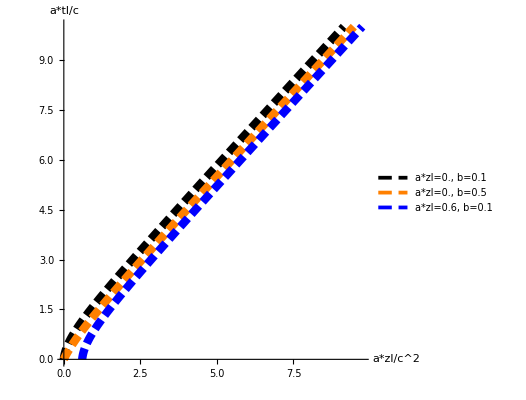

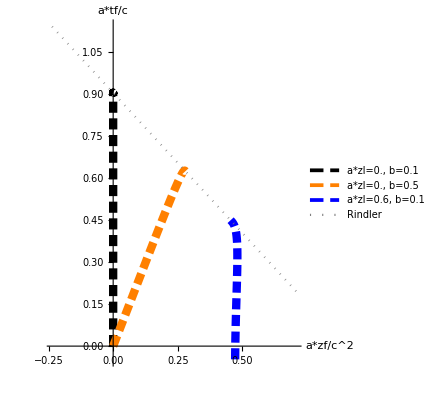

```mathematica
(* Motion of "0" and "1" due to force alone *)
(* linestyle *)
ls=Directive[Dashing[{0.02,0.01}],Thickness[0.015]];
lsE={Directive[Black,ls],Directive[Orange,ls],Directive[Blue,ls]};
(* Make plots *)
{plE,pfE}=ZLtPlotList[tmax,w00,a00,0,0,zlblist1,lsE,a00];
Show[plE]
Show[pfE]
```

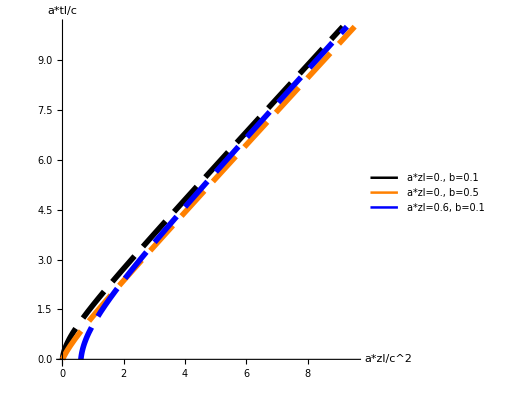

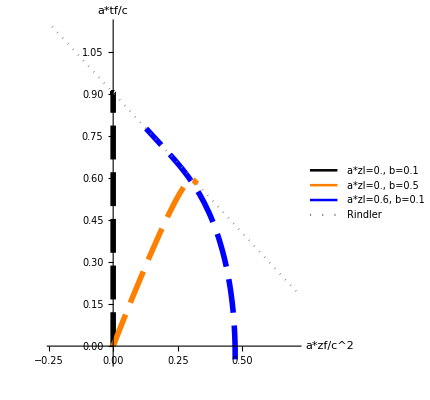

```mathematica
(* Motion of "0" and "1" due to mass alone *)
(* linestyle *)
ls=Directive[Dashing[{0.061,0.023}],Thickness[0.01]];
lsM={Directive[Black,ls],Directive[Orange,ls],Directive[Blue,ls]};
(* Make plots *)
{plM,pfM}=ZLtPlotList[tmax,w00,0,0,a00,zlblist1,lsM,a00];
Show[plM]
Show[pfM]
```

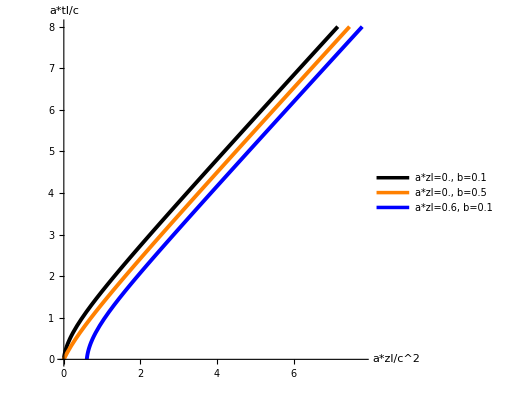

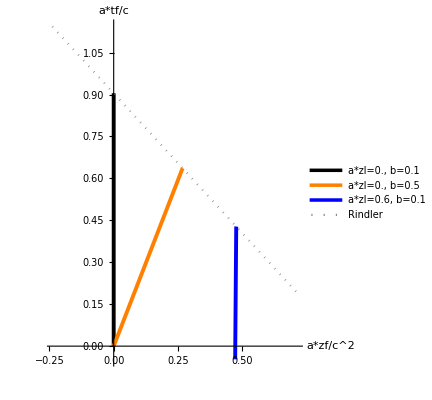

```mathematica
(* Motion of "0" and "1" due to metric alone *)
(* linestyle *)
ls=Directive[Thickness[0.007]];
lsG={Directive[Black,ls],Directive[Orange,ls],Directive[Blue,ls]};
(* Make plots *)
{plG,pfG}=ZLtPlotList[tmax*0.8,w00,0,a00,0,zlblist1,lsG,a00];
Show[plG]
Show[pfG]
```

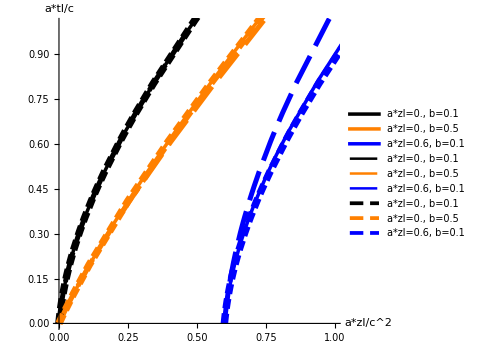

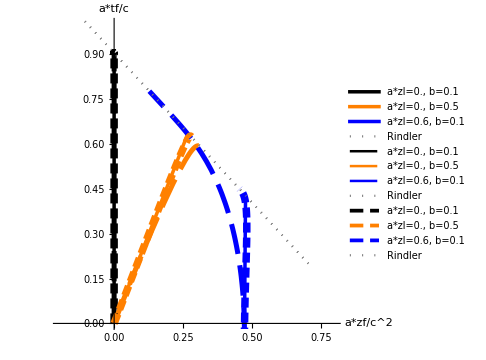

```mathematica
Show[Flatten[{plG,plM,plE}],PlotRange->{{0,1},{0,1}},AspectRatio->1,ImageSize->360]
Show[Flatten[{pfG,pfM,pfE}],PlotRange->{{-0.2,0.8},{0,1}},AspectRatio->1,ImageSize->360]
```

```mathematica
(*****************************************)
(* Initial acceleration of test particles *)
(*****************************************)
```

```mathematica
(* Plot Exact and asymptotics residual accelerations *)
(* for two cases (1) z1=z0, (2) b1=0 *)
(* Set aE0=-(aG0+aM0/Cosh[w0]) to cancel leading acceleration at zl=0 and b=0, the remaining acceleration is the residual acceleration *)
(* a0 is the total acceleration *)
(* fGlist={fG1, fG1,...} is fractional acceleration in metric, namely, *)
(* aG0=a0*fG, aM0=(1-fG)*a0 *)
(* clist={ls1, ls2, ...lsN} is a list of plot colors *)
aRPlotList[w0_,a0_,fGlist_,clist_,ahmax_]:=Module[
{nc,pzlist,pblist,w00,ic,fG,aG0,aM0,aE0,label,lss,lsd,pz,pb,b1,ah1},
(* Dimension of list *)
nc=Length[fGlist];
(* Initialize plots for both cases*)
pzlist={};pblist={};(* plots *)
(* In special case w0=0, replace w0 by a small number to avoid indeterminate behavior of Azb *)
If[w0==0,
w00=10^(-6);
Print["In Azb, replaced w0=0 by 10^(-6) to avoid indeterminate behavior"],
w00=w0];
For[ic=1,ic≤nc,ic++,
(* unpack for this case *)
fG=fGlist[[ic]];
aG0=a0*fG;
aM0=(1-fG)*a0;
aE0=-aG0-aM0/Cosh[w0];
label=Row[{"aG0/a0=",fG}];
lss=Directive[clist[[ic]],Thickness[0.01]];
lsd=Directive[clist[[ic]],Thickness[0.015],Dashed];
(* z1=z0, exact and asymptotics *)
pz=Show[Plot[Azb[0,b1,w00,aE0,aG0,aM0]/a0,{b1,0,1},PlotStyle->lss,PlotLegends->{label},AxesLabel->{"b1","ar/a0"}],Plot[aRz[b1,w0,aG0,aM0]/a0,{b1,0,0.7},PlotStyle->lsd]];
(* b1=0, exact and asymptotics*)
pb=Show[Plot[Azb[ah1/a0,0,w00,aE0,aG0,aM0]/a0,{ah1,0,ahmax},PlotStyle->lss,PlotLegends->{label},AxesLabel->{"a0*h1/c^2","ar/a0"}],Plot[aRb[ah1/a0,w0,aG0,aM0]/a0,{ah1,0,ahmax/2},PlotStyle->lsd]];
(* Store solution and figures for this particle *)
AppendTo[pzlist,pz];
AppendTo[pblist,pb];
];
Return[{pzlist,pblist}]
]
```

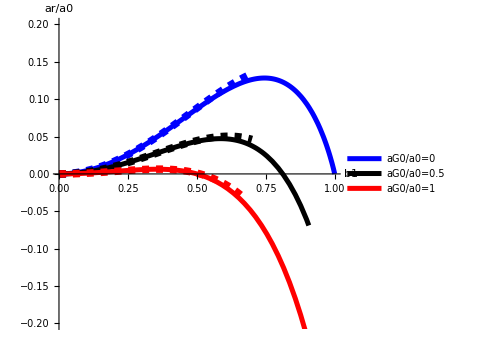

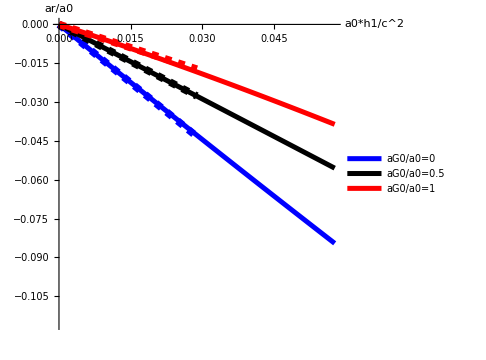

```mathematica
(* Initial conditions for particle "0" *)
b00=0.5; (* When b0≠0, asymptotics valid for a*h<<Sinh[w0] *)
(* Common acceleration *)
a00=0.2;
(* fractional acceleration due to metric *)
ahmax0=Sinh[ArcTanh[b00]]/10;
fGlist1={0,0.5,1};
clist1={Blue,Black,Red};
(* Plot figures *)
{pzlist,pblist}=aRPlotList[ArcTanh[b00],a00,fGlist1,clist1,ahmax0];
Show[pzlist,PlotRange->{{0,1},{-0.2,0.2}},AspectRatio->1,ImageSize->360]
Show[pblist,PlotRange->{{0,ahmax0},{-2ahmax0,0}},AspectRatio->1,ImageSize->360]
```

In Azb, replaced w0=0 by 10^(-6) to avoid indeterminate behavior

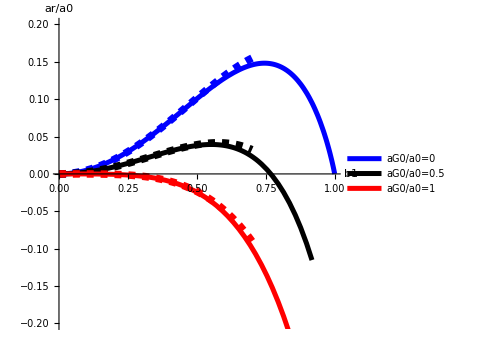

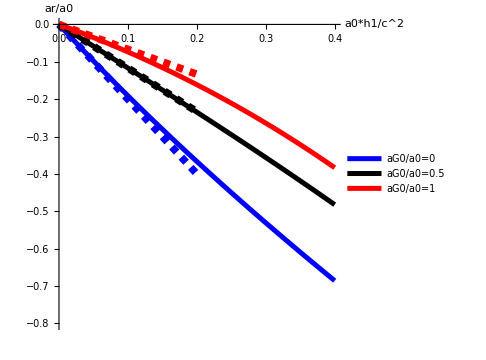

```mathematica
(* Initial conditions for particle "0" *)
(* Special case b0==0 *)
(* Common acceleration *)
a00=0.2;
(* fractional acceleration due to metric *)
ahmax0=0.4;
fGlist1={0,0.5,1};
clist1={Blue,Black,Red};
(* Plot figures *)
{pzlist,pblist}=aRPlotList[0,a00,fGlist1,clist1,ahmax0];
Show[pzlist,PlotRange->{{0,1},{-0.2,0.2}},AspectRatio->1,ImageSize->360]
Show[pblist,PlotRange->{{0,ahmax0},{-2ahmax0,0}},AspectRatio->1,ImageSize->360]
```